## 136Nd - Petrache Study

## All structures

-Graphics-

According to Ref. “Evolution from y-soft to stable triaxiality in 136 Nd as a prerequisite of chirality”, the bands [3,4] are [L7, unknown]

```mathematica
ClearAll["Global`*"]
```

```mathematica
(* the quasi-hole configuration *)
band3En=Sort[N[#/1000]&@{5841,4847,3995,3277}];
band4En=Sort[N[#/1000]&@{5346,4545,4026}];
band3Spins=Table[i,{i,10,16,2}];
band4Spins=Table[i,{i,11,15,2}];
(* the quasi-particle configuration *)
band2En=Sort[N[#/1000]&@{8615,7349,6188,5189,4345,3684,3294}];
band5En=Sort[N[#/1000]&@{8098,6928,5940,5130,4452}];
band6En=Sort[N[#/1000]&@{9171,8222,7329,6470,5568,4853}];
band2Spins=Table[i,{i,10,22,2}];
band5Spins=Table[i,{i,13,21,2}];
band6Spins=Table[i,{i,14,24,2}];
```

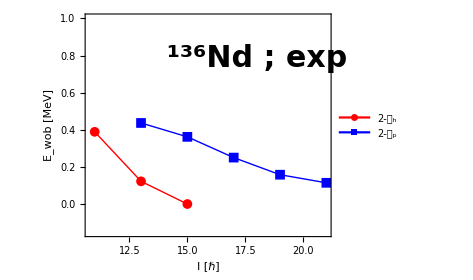

```mathematica
m1minipath="/Users/basavyr/Documents/DevWorkspace/GitHub/mathematica-useful-algorithms/Physics/experimental-data-collection-wobblers/Nd-Nuclei/136Nd-joint.pdf";
wobbling1[yrast_,onephonon_,onespins_]:=Table[{onespins[[i]],onephonon[[i]]-1/2(yrast[[i]]+yrast[[i+1]])},{i,1,Length[onephonon]}];
wobbling2[yrast_,onephonon_,onespins_]:=Table[{onespins[[i]],onephonon[[i]]-1/2(yrast[[i+1]]+yrast[[i+2]])},{i,1,Length[onephonon]}];
data1=wobbling1[band3En,band4En,band4Spins];
data2=wobbling2[band2En,band5En,band5Spins];
fig=ListPlot[{data1,data2},Joined->True,PlotMarkers->{Automatic, Medium},Frame->True,Axes->False,AspectRatio->0.8,PlotStyle->{{Red,Thick},{Blue,Thick}},FrameStyle->Directive[Thick,Black],FrameLabel->{"I [ℏ]","E_wob [MeV]"},LabelStyle->{20,Bold,Black,FontFamily->"Arial"},ImageSize->350,PlotRange->{Full,{-0.15,1}},PlotLegends->Placed[{Style["2-𝒬_h",24],Style["2-𝒬_p",24]},{0.2,0.8}],Epilog->{Inset[Style[Row[{Superscript["","136"],"Nd ; exp"}],Bold ,FontFamily->"Arial",30],Scaled[{0.7,0.8}]]}];
Export[m1minipath,fig];
Show[fig]
```